# Accuracy of Normal approximation for binomial inversion

### Set - up

High precision needed to work with full double precision range from 10^-308 to 1-10^-308

```mathematica
(* Set machine precision at start *)
(* Uncomment if we want arbitrary precision throughout *)

$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`400."&);
```

```mathematica
(* Matlab style linspace and logspace *)
linspace[start_,stop_,n_:100]:=start + (stop-start)*Subdivide[n-1];
linspace[start_,stop_,1]:=stop;
logspace[start_,stop_,n_:100]:=10.0^linspace[start,stop,n];
```

### Error as a function of x for varying M and fixed p

Define range of x and the value of p

```mathematica
(* Succes probability p *)
p =0.25;
(* Range of x values. Note that for x<10 we always use direct summation and thus do not rely on Normal approximation*)
xmin = 10;
xs = logspace[Log10[xmin],Log10[xmin]+8,20];
(* Round up xs to integer values *)
xs = Ceiling[xs];
```

Find limits for the normal distribution given x, i.e. for what value of M do we have P(k ≤ x|M,p)<F_N(-3) ≃0.00135 and P(k ≥ x|M,p)<F_N(3) ≃0.99865

```mathematica
W = linspace[-3.,3.,2];
U = CDF[NormalDistribution[0,1],W];
(* Initialize arrays to save data in *)
Mbounds = Table[,{j,Length[xs]}];
Do[
(* Upper limit for M, i.e. for w=-3 *)
M1 =m/.FindRoot[BetaRegularized[1-p,m-xs[[ix]]+1,xs[[ix]]]==U[[1]],{m,xs[[ix]]-1,10*xs[[ix]]/p},WorkingPrecision->100, MaxIterations->1000][[1]];
(* Lower limit for M, i.e. for w=3. Note we use the relation Subscript[I, 1-p](m-x+1,x) = 1-Subscript[I, p](x,m-x+1) *)
M2 = m/.FindRoot[BetaRegularized[p,xs[[ix]],m-xs[[ix]]+1]==U[[1]],{m,xs[[ix]]-1,10*xs[[ix]]/p},WorkingPrecision->100,MaxIterations->1000][[1]];
(* Note that the lower and upper limit needs to satisfy Mp≥Subscript[μ, 0], M(1-p)≥Subscript[μ, 0] in order to be done via the Normal approximation *)
Subscript[μ, 0]=10;
M2 = Max[{Subscript[μ, 0]/p,Subscript[μ, 0]/(1-p),M2}];
M1 = Max[{Subscript[μ, 0]/p,Subscript[μ, 0]/(1-p),M1}];
Mbounds[[ix]] = {M1,M2};
,{ix,Length[xs]}];
```

Normal approximation functions

```mathematica
Q0[m_,p_,w_]:=m*p+Sqrt[m*p*(1-p)]*w;
Q1[m_,p_,w_] := Q0[m,p,w] + (p+1)/3 +(1-2*p)*w^2/6;
Q2[m_,p_,w_] := Q1[m,p,w] + (-(7*p^2-7*p+1)*w/36 + (2*p^2-2*p-1)*w^3/72)/Sqrt[m*p*(1-p)];
Q3[m_,p_,w_] := Q2[m,p,w]+((1-2*p)*(p+1)*(2-p)*(3*w^4+7*w^2-16)/1620)/(m*p*(1-p));
fdelta[m_,p_,w_] := ((1/4)/Sqrt[m*p*(1-p)]+Abs[1-2*p])*((2-p)*(p+1)*(4*w^4+8*w^2+16)/1600)/(m*p*(1-p));
```

Iterate over the values of x to get the error in the normal approximation

```mathematica
nU = 30;
err = Table[,{i,4},{j,Length[xs]}];
rerr = Table[,{j,Length[xs]}];
Msave = Table[,{j,Length[xs]}];
Wsave = Table[,{j,Length[xs]}];
Do[
(* Construct a range of M valid for x *)
If[Mbounds[[ix,1]]≤ Mbounds[[ix,2]],
(* If upper limit for M is less than lower limit for M we can't do anything, i.e. Normal approximation is never used for this xs, p combination *)
M={},
(* Otherwise construct a linear spaced array *)
M =Floor[linspace[Mbounds[[ix,1]],Mbounds[[ix,2]],nU]];
(* Given M and x we calculate the values of w used *)
W = InverseCDF[NormalDistribution[0,1],Table[BetaRegularized[1-p,m-xs[[ix]]+1,xs[[ix]]],{m,M}]];
(* Construct the normal approximations *)
X1 = Q0[M,p,W];
X2 = Q1[M,p,W];
X3 = Q2[M,p,W];
X4 = Q3[M,p,W];
dX = fdelta[M,p,W];
err[[1,ix]] = xs[[ix]]-X1;
err[[2,ix]] = xs[[ix]]-X2;
err[[3,ix]] = xs[[ix]]-X3;
err[[4,ix]] = xs[[ix]]-X4;
rerr[[ix]] = (xs[[ix]]-X3)/dX;
Wsave[[ix]] = W;
];
Msave[[ix]] = M;
,{ix,Length[xs]}]
```

Plot the error for a fixed x as a function of M for the range |w|≤3 (cf. Fig. 2 Giles 2015 paper )

1.×10^9

0.5

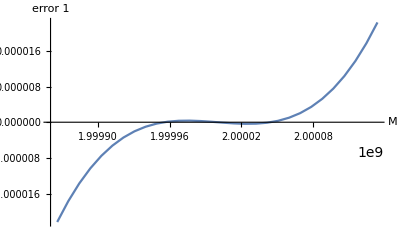

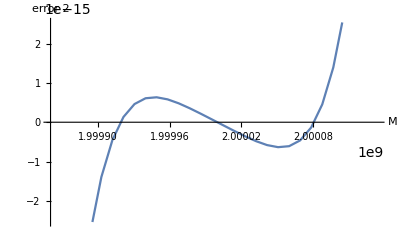

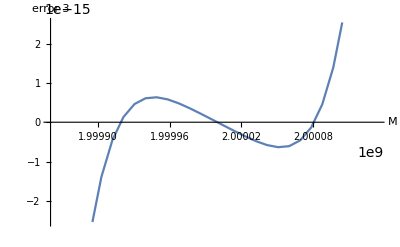

```mathematica
idxplot = 20;
N[xs[[idxplot]],4]
N[p,3]
ListPlot[Transpose[{Msave[[idxplot]],err[[2,idxplot]]}],Joined->True,AxesLabel->{"M","error 1"}]
ListPlot[Transpose[{Msave[[idxplot]],err[[3,idxplot]]}],Joined->True,AxesLabel->{"M","error 2"}]
ListPlot[Transpose[{Msave[[idxplot]],err[[4,idxplot]]}],Joined->True,AxesLabel->{"M",
"error 3"}]
```

Plot the maximum relative difference between X3-x and the dX error for given w in the correct range.

10.

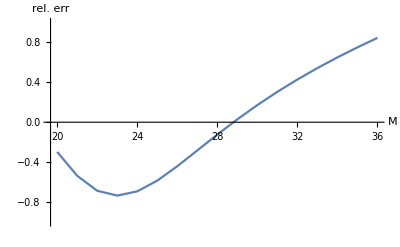

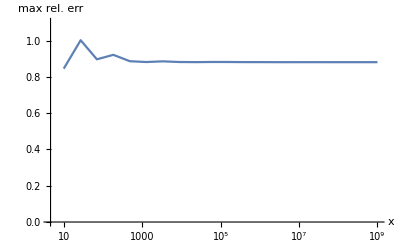

1.

```mathematica
(* First for a given x fixed *)
idxplot =1;
N[xs[[idxplot]],4]
ListPlot[Transpose[{Msave[[idxplot]],rerr[[idxplot]]}],Joined->True,AxesLabel->{"M","rel. err"},PlotRange->{Full,{-1,1}}]
(* Then over the range of all x taken the max for each fixed x *)
(* Find array with max relative error, also used to save *)
Rerr = Table[Max[Abs[rerr[[ix]]]],{ix,Length[xs]}]/.Abs[Null]->Null;
ListLogLinearPlot[Transpose[{xs,Rerr}],Joined->True,PlotRange->{Full,{0.0,1.1}},(*PlotRange->{Full,{Min[DeleteCases[Rerr,Null]]*0.9,1.01}},*)AxesLabel->{"x","max rel. err"},GridLines->{{{10,Dashed}}, {{1,Dashed}}}]
N[Max[Rerr],3]
```

Look at the maximum error for given x

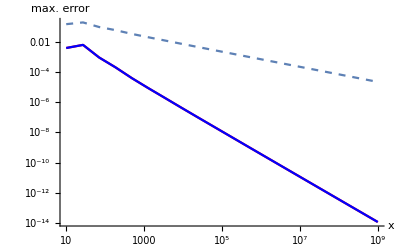

```mathematica
maxerr = Table[Max[Abs[err[[jx,ix]]]],{jx,4},{ix,Length[xs]}]/.Abs[Null]->Null;
p1 = ListLogLogPlot[Transpose[{xs,maxerr[[1,All]]}]];
p2 = ListLogLogPlot[Transpose[{xs,maxerr[[2,All]]}],PlotStyle->{Dashed},Joined->True];
p3 = ListLogLogPlot[Transpose[{xs,maxerr[[3,All]]}],PlotStyle->Red,Joined->True];
p4 = ListLogLogPlot[Transpose[{xs,maxerr[[4,All]]}],PlotStyle->Blue,Joined->True];
Show[p2,p3,p4,PlotRange->Full,AxesLabel->{"x","max. error"}]
```

Export to Matlab readable data

```mathematica
idxValid = Table[m*p> 4&& m*(1-p)> 4 && m> 100,{m,Mbounds[[All,2]]}];
rerrExport=Pick[Rerr,idxValid,True];
xsExport = Pick[xs,idxValid,True];
errExport = Table[Pick[maxerr[[j]],idxValid,True],{j,4}];
MExport = Pick[Msave,idxValid,True];
WExport = Pick[Wsave,idxValid,True];
```

```mathematica
(* Prune the data to only include x for which w can take the full range of values *)
SetDirectory[NotebookDirectory[]];
Export["mathematicadataRelativeError.mat",MatrixForm[rerrExport],"Data"];
Export["mathematicadataError.mat",MatrixForm[errExport],"Data"];
Export["mathematicadataM.mat",MatrixForm[MExport],"Data"];
Export["mathematicadatap.mat",MatrixForm[p],"Data"];
Export["mathematicadataW.mat",MatrixForm[WExport],"Data"];
Export["mathematicadataxs.mat",MatrixForm[xsExport],"Data"];
Export["mathematicadatadelta.mat",MatrixForm[dX],"Data"];
```

### Error as a function of M for varying x and fixed p

Define range of x and the value of p

```mathematica
(* Succes probability p *)
p =0.25;
(* Range of x values. Note that for x<10 we always use direct summation and thus do not rely on Normal approximation*)
Mmin = Max[{10/p,10/(1-p)}];
M = logspace[Log10[Mmin],Log10[Mmin]+8,20];
(* Round up xs to integer values *)
M = Ceiling[M];
```

Normal approximation functions

```mathematica
Q0[m_,p_,w_]:=m*p+Sqrt[m*p*(1-p)]*w;
Q1[m_,p_,w_] := Q0[m,p,w] + (p+1)/3 +(1-2*p)*w^2/6;
Q2[m_,p_,w_] := Q1[m,p,w] + (-(7*p^2-7*p+1)*w/36 + (2*p^2-2*p-1)*w^3/72)/Sqrt[m*p*(1-p)];
Q3[m_,p_,w_] := Q2[m,p,w]+((1-2*p)*(p+1)*(2-p)*(3*w^4+7*w^2-16)/1620)/(m*p*(1-p));
fdelta[m_,p_,w_] := ((1/4)/Sqrt[m*p*(1-p)]+Abs[1-2*p])*((2-p)*(p+1)*(4*w^4+8*w^2+16)/1600)/(m*p*(1-p));

(* Cornish-Fisher expansion of O(n^-1/2) *)
Q2CF[m_,p_,w_]:=Q1[m,p,w] + (1/72 (1-14 (-1+p) p) w+1/72 (-1+2 (-1+p) p) w^3)/Sqrt[m*p*(1-p)];
```

Iterate over the values of x to get the error in the normal approximation

```mathematica
nU = 31;
err = Table[,{i,5},{j,Length[M]}];
rerr = Table[,{j,Length[M]}];
Xsave = Table[,{j,Length[M]}];
Wsave = Table[,{j,Length[M]}];
Do[
m=M[[ix]];
W= linspace[-3.,3.,nU];
U = CDF[NormalDistribution[0,1],W];
xs =Table[ x/.FindRoot[BetaRegularized[1-p,m-x+1,x]==U[[ix]],{x,0,m},WorkingPrecision->50,MaxIterations->1000][[1]],{ix,nU}];
(* Construct the normal approximations *)
X1 = Q0[m,p,W];
X2 = Q1[m,p,W];
X3CF = Q2CF[m,p,W];
X3 = Q2[m,p,W];
X4 = Q3[m,p,W];
dX = fdelta[m,p,W];
err[[1,ix]] = xs-X1;
err[[2,ix]] = xs-X2;
err[[3,ix]] = xs-X3;
err[[4,ix]] = xs-X4;
err[[5,ix]]=xs-X3CF;
rerr[[ix]] = (xs-X3)/dX;
Wsave[[ix]] = W;
Xsave[[ix]] = xs;
,{ix,Length[M]}]
```

Plot the error for a fixed M as a function of w for the range |w|≤3

4.×10^9

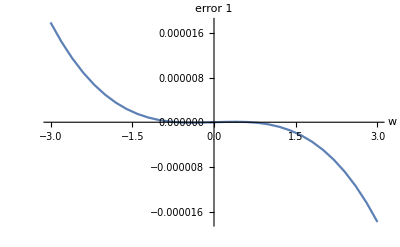

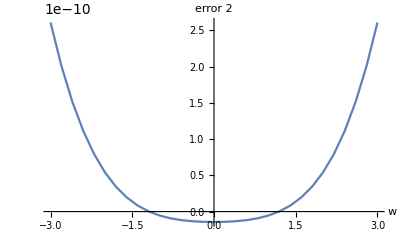

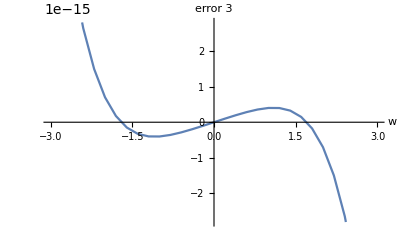

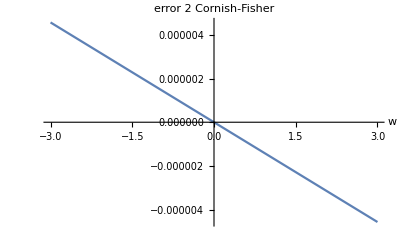

```mathematica
idxplot = 20;
N[M[[idxplot]],4]
ListPlot[Transpose[{Wsave[[idxplot]],err[[2,idxplot]]}],Joined->True,AxesLabel->{"w","error 1"}]
ListPlot[Transpose[{Wsave[[idxplot]],err[[3,idxplot]]}],Joined->True,AxesLabel->{"w","error 2"}]
ListPlot[Transpose[{Wsave[[idxplot]],err[[4,idxplot]]}],Joined->True,AxesLabel->{"w",
"error 3"}]
ListPlot[Transpose[{Wsave[[idxplot]],err[[5,idxplot]]}],Joined->True,AxesLabel->{"w",
"error 2 Cornish-Fisher"}]
```

Plot the maximum relative difference between X3-x and the dX error for given w in the correct range.

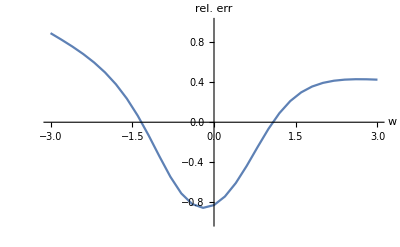

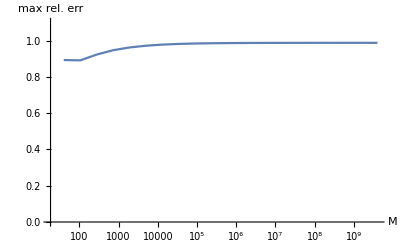

9.999×10^8

0.988

```mathematica
(* First for a given x fixed *)
idxplot =1;

ListPlot[Transpose[{Wsave[[idxplot]],rerr[[idxplot]]}],Joined->True,AxesLabel->{"w","rel. err"},PlotRange->{Full,{-1,1}}]
(* Then over the range of all x taken the max for each fixed x *)
(* Find array with max relative error, also used to save *)
Rerr = Table[Max[Abs[rerr[[ix]]]],{ix,Length[M]}]/.Abs[Null]->Null;
ListLogLinearPlot[Transpose[{M,Rerr}],Joined->True,PlotRange->{Full,{0.0,1.1}},(*PlotRange->{Full,{Min[DeleteCases[Rerr,Null]]*0.9,1.01}},*)AxesLabel->{"M","max rel. err"},GridLines->{{{10,Dashed}}, {{1,Dashed}}}]
N[xs[[idxplot]],4]
N[Max[Rerr],3]
```

Look at the maximum error for given x

```mathematica
maxerr = Table[Max[Abs[err[[jx,ix]]]],{jx,5},{ix,Length[M]}]/.Abs[Null]->Null;
p1 = ListLogLogPlot[Transpose[{M,maxerr[[1,All]]}]];
p2 = ListLogLogPlot[Transpose[{M,maxerr[[2,All]]}],PlotStyle->{Dashed},Joined->True,PlotLabels->"Q-Q_N1"];
p3 = ListLogLogPlot[Transpose[{M,maxerr[[3,All]]}],PlotStyle->Red,Joined->True,PlotLabels->"Q-Q_N2"];
p4 = ListLogLogPlot[Transpose[{M,maxerr[[4,All]]}],PlotStyle->Blue,Joined->True,PlotLabels->"Q-Q_N3"];
p5 = ListLogLogPlot[Transpose[{M,maxerr[[5,All]]}],PlotStyle->Green,Joined->True,PlotLabels->"Q-Q_N2(Cornish-Fisher)"];
Show[p1,p2,p3,p4,p5,PlotRange->Full,AxesLabel->{"M","max. error"}]
```

-Graphics-

### Bound on δ

First we check whether δ<1/2 holds for all p and M. Note that δ is largest when M ·p or M·(1-p) is small so we only need to check for the extreme cases (i.e. M·p=μ_0 and M·(1-p)=μ_0)

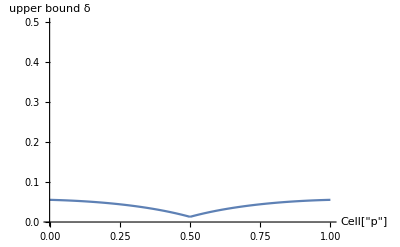

(103 (1+1/(4 √10)))/2000

0.0555714

```mathematica
Subscript[μ, 0]=10;
Plot[fdelta[Max[Subscript[μ, 0]/p,Subscript[μ, 0]/(1-p)],p,3],{p,0,1},PlotRange->{Full,{0,0.5}},AxesLabel->{"Cell["p",ExpressionUUID->"8e83b448-ea23-481a-aff8-2c451061e4b8"]","upper bound δ"}]
(* Max value of δ when p→0 or p→1 *)
Limit[fdelta[Subscript[μ, 0]/q,q,3],q->0,Direction->"FromAbove"]
N[Limit[fdelta[Subscript[μ, 0]/q,q,3],q->0,Direction->"FromAbove"]]
```

Expected value of δ using E[w^2]=1 and E[w^4]=3

```mathematica
gdelta[m_,p_]:=SeriesCoefficient[fdelta[m,p,w],{w,0,0}] +SeriesCoefficient[fdelta[m,p,w],{w,0,2}] *1+ SeriesCoefficient[fdelta[m,p,w],{w,0,4}]*3
```

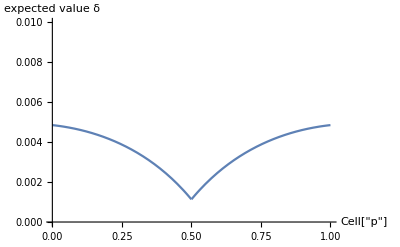

(9 (1+1/(4 √10)))/2000

0.00485576

```mathematica
Plot[gdelta[Max[Subscript[μ, 0]/p,Subscript[μ, 0]/(1-p)],p],{p,0,1},PlotRange->{Full,{0,0.01}},AxesLabel->{"Cell["p",ExpressionUUID->"da53f371-f137-4ea9-bc2c-7ffbcd46063a"]","expected value δ"}]
(* Max value of expected value of δ when p→0 or p→1 *)
Limit[gdelta[Subscript[μ, 0]/P,P],P->0,Direction->"FromAbove"]
N[Limit[gdelta[Subscript[μ, 0]/P,P],P->0,Direction->"FromAbove"]]
```

Probability to need a check is ~2δ

```mathematica
2*N[Limit[gdelta[Subscript[μ, 0]/P,P],P->0,Direction->"FromAbove"]]
```

0.00971151

Check what is necessary to get the δ formula working for p=1/2 by scaling the δ derived from comparing Q_N2 and Q_N3

```mathematica
(* Difference between asymptotic series of order 3 and 2 *)
fN2N3[m_,p_,w_]:=-((3*w^4+7*w^2-16)*(-2*p^3+3*p^2+3*p-2))/(1620*m p*(1-p));
(* Difference between asymptotic series of order 4 and 3 *)
fN3N4[m_,p_,w_]:=-(w*(-36*p^4*w^4-1024*p^4*w^2+1732*p^4+72*p^3*w^4+2048*p^3*w^2-3464*p^3+432*p^2*w^4+588*p^2*w^2-3684*p^2-468*p*w^4-1612*p*w^2+5416*p+207*w^4+548*w^2-2684))/(155520*m^(3/2)*p^(3/2)*(1-p)^(3/2));
(* Difference between asymptotic series of order 5 and 4 *)
fN4N5[m_,p_,w_]:=-((2*p-1)*(12*p^4*w^6-243*p^4*w^4-923*p^4*w^2+1472*p^4-24*p^3*w^6+486*p^3*w^4+1846*p^3*w^2-2944*p^3+252*p^2*w^6+945*p^2*w^4-5271*p^2*w^2-1344*p^2-240*p*w^6-1188*p*w^4+4348*p*w^2+2816*p+228*w^6+675*w^4-5189*w^2-256))/(408240*m^2p^(2)*(1-p)^(2));
(* Difference between asymptotic series of order 6 and 5 *)
fN5N6[m_,p_,w_]:=
-(w*(30024*p^6*w^6+34824*p^6*w^4-2316136*p^6*w^2-2317736*p^6-90072*p^5*w^6-104472*p^5*w^4+6948408*p^5*w^2+6953208*p^5+597132*p^4*w^6+3277872*p^4*w^4-19643388*p^4*w^2-28633728*p^4-1044144*p^3*w^6-6381624*p^3*w^4+27706096*p^3*w^2+45678776*p^3+1668762*p^2*w^6+7683462*p^2*w^4-51040068*p^2*w^2-38491968*p^2-1161702*p*w^6-4510062*p*w^4+38345088*p*w^2+16811448*p+303399*w^6+994674*w^4-10591636*w^2-2198936))/(1175731200*(m*p*(1-p))^(5/2));
```

```mathematica
β=1/3;
Manipulate[Manipulate[Plot[{(1+p)(2-p)*(Abs[1-2p]+β/Sqrt[m p (1-p)])(1/100+w^2/200 + w^4/400)/(m p(1-p)),Abs[Simplify[fN2N3[m,p,w]]],Abs[Simplify[fN3N4[m,p,w]]],Abs[Simplify[fN4N5[m,p,w]]],Abs[Simplify[fN5N6[m,p,w]]],Abs[Simplify[fN2N3[m,p,w]+fN3N4[m,p,w]+fN4N5[m,p,w]+fN5N6[m,p,w]]]},{w,-3,3},PlotLegends->{"δ","Q_N3-Q_N2","Q_N4-Q_N3","Q_N5-Q_N4","Q_N6-Q_N5","Q_N6-Q_N2"},PlotRange->Full],{m,Max[10./p,10./(1-p)],Max[10./p,10./(1-p)]+1000000}],{p,10.^-7,1-10.^-7}]
```

How close can the true error get to δ for a specific combination of M and p

```mathematica
W = linspace[-3.,3.,100];
U = CDF[NormalDistribution[0,1],W];
(* Initialize arrays to save data in *)
M = 37;
p = 0.49999995;
(* Initialize arrays to save data in *)
exactD = Table[,{j,Length[W]}];
rexactD = Table[,{j,Length[W]}];
Do[
(* Exact Q(u) *)
Q =x/.FindRoot[BetaRegularized[1-p,M-x+1,x]==U[[ix]],{x,0,M},WorkingPrecision->100, MaxIterations->1000][[1]];
(* Error between Q(u) and Subscript[Q, N2](u) *)
(* Note that we only consider the error if 10<Q<M-10 as otherwise we would use direct summation*)
exactD[[ix]] = If[Q<10||M-Q < 10,0,Abs[Q - Q2[M,p,W[[ix]]]]];
rexactD[[ix]] = exactD[[ix]]/fdelta[M,p,W[[ix]]];
,{ix,Length[W]}];
p1 = ListPlot[Transpose@{W,exactD},PlotStyle->Red,PlotLabels->{"true error"}];
p2=Plot[fdelta[M,p,w],{w,Min[W],Max[W]},PlotLabels->{"δ"}];
Show[p1,p2,PlotRange->Full,AxesLabel->{"w",None}]
N[Max[rexactD],3]
```

-Graphics-

0.925

### Inverse asymptotic expansion coefficients

```mathematica
f[x_,y_]:= f0[x]+f1[x]y+f2[x]y^2+f3[x]y^3+f4[x]y^4+f5[x]y^5+f6[x]y^6+f7[x]y^7;
g[x_,y_]:= g0[x]+g1[x]y+g2[x]y^2+g3[x]y^3+g4[x]y^4+g5[x]y^5+g6[x]y^6+g7[x]y^7;
```

```mathematica
Simplify[SeriesCoefficient[g[f[x,y],y],{y,0,1}]]
```

g1[f0[x]]+f1[x] g0'[f0[x]]

```mathematica
Simplify[SeriesCoefficient[g[f[x,y],y],{y,0,2}]]
```

g2[f0[x]]+f2[x] g0'[f0[x]]+f1[x] g1'[f0[x]]+1/2 f1[x]^2 g0''[f0[x]]

```mathematica
Simplify[SeriesCoefficient[g[f[x,y],y],{y,0,3}]]
```

g3[f0[x]]+f3[x] g0'[f0[x]]+f2[x] g1'[f0[x]]+f1[x] g2'[f0[x]]+f1[x] f2[x] g0''[f0[x]]+1/2 f1[x]^2 g1''[f0[x]]+1/6 f1[x]^3 g0^(3)[f0[x]]

```mathematica
Simplify[SeriesCoefficient[g[f[x,y],y],{y,0,4}]]
```

g4[f0[x]]+f4[x] g0'[f0[x]]+f3[x] g1'[f0[x]]+f2[x] g2'[f0[x]]+f1[x] g3'[f0[x]]+1/2 (f2[x]^2+2 f1[x] f3[x]) g0''[f0[x]]+f1[x] f2[x] g1''[f0[x]]+1/2 f1[x]^2 g2''[f0[x]]+1/2 f1[x]^2 f2[x] g0^(3)[f0[x]]+1/6 f1[x]^3 g1^(3)[f0[x]]+1/24 f1[x]^4 g0^(4)[f0[x]]

```mathematica
Simplify[SeriesCoefficient[g[f[x,y],y],{y,0,5}]]
```

g5[f0[x]]+f5[x] g0'[f0[x]]+f4[x] g1'[f0[x]]+f3[x] g2'[f0[x]]+f2[x] g3'[f0[x]]+f1[x] g4'[f0[x]]+f2[x] f3[x] g0''[f0[x]]+f1[x] f4[x] g0''[f0[x]]+1/2 f2[x]^2 g1''[f0[x]]+f1[x] f3[x] g1''[f0[x]]+f1[x] f2[x] g2''[f0[x]]+1/2 f1[x]^2 g3''[f0[x]]+1/2 f1[x] f2[x]^2 g0^(3)[f0[x]]+1/2 f1[x]^2 f3[x] g0^(3)[f0[x]]+1/2 f1[x]^2 f2[x] g1^(3)[f0[x]]+1/6 f1[x]^3 g2^(3)[f0[x]]+1/6 f1[x]^3 f2[x] g0^(4)[f0[x]]+1/24 f1[x]^4 g1^(4)[f0[x]]+1/120 f1[x]^5 g0^(5)[f0[x]]

### Cornish-Fisher expansion comparison

```mathematica
Clear[m,p]
```

Probabilists Hermite polynomials and Cornish-Fisher coefficients

```mathematica
He[x_,n_]:=2^(-n/2)*HermiteH[n,x/Sqrt[2]]
gam[n_,M_,p_]:=Cumulant[BinomialDistribution[M,p],n+2]/(Cumulant[BinomialDistribution[M,p],2]^((n+2)/2))
```

Second order Cornish-Fisher expansion + continuity correction of 1/2

```mathematica
CFexp = FullSimplify[1/2+Sqrt[m p (1-p)]*(gam[1,m,p]*He[w,2]/6 +gam[2,m,p]*He[w,3]/24 + gam[1,m,p]^2*(-(2*He[w,3]+He[w,1])/36) + gam[3,m,p]*He[w,4]/120 + gam[1,m,p]*gam[2,m,p]*(-(He[w,4]+He[w,2])/24) + gam[1,m,p]^3*(12*He[w,4] + 19*He[w,4])/324)/.{m->σ^2/(p(1-p))},{σ>0,0<p<1,-3<w<3}];
```

O(1) term

```mathematica
Collect[SeriesCoefficient[CFexp,{σ,Infinity,0}],w,Simplify]
```

(1+p)/3+1/6 (1-2 p) w^2

O((n p (1-p))^(-1/2)) term. Note this is different from same term in Normal asymptotic approximation (by a factor -3 w/(72√(n p(1-p) )) ).

```mathematica
Collect[SeriesCoefficient[CFexp,{σ,Infinity,1}],w,Simplify]
```

1/72 (1-14 (-1+p) p) w+1/72 (-1+2 (-1+p) p) w^3

O((n p (1-p))^-1)term (apart from (1-2 p) term this is quite different from Normal asymptotic approximation ).

```mathematica
FullSimplify[Collect[SeriesCoefficient[CFexp,{σ,Infinity,2}],w,Simplify]]
```

-((-1+2 p) (741+3072 (-1+p) p-1347 w^2-5334 (-1+p) p w^2+2 (101+377 (-1+p) p) w^4))/3240